```mathematica
z = PauliMatrix[3];
x = PauliMatrix[1];
I1 = IdentityMatrix[2];
I2 = IdentityMatrix[2^2];
I3 = IdentityMatrix[2^3];
I4 = IdentityMatrix[2^4];
```

```mathematica
(*-----------------------------------------------------------------------------------------------------*)
```

```mathematica
(*---------------------------------------------3-leg, 1-rung MF----------------------------------------*)
```

```mathematica
(*-----------------------------------------------------------------------------------------------------*)
```

```mathematica
H31= -2m(KroneckerProduct[z,I1] + KroneckerProduct[I1,z]) -Δ(KroneckerProduct[x,I1]+ KroneckerProduct[I1,x] + τ KroneckerProduct[x,x])//MatrixForm
```

(-4 m | -Δ | -Δ | -Δ τ
-Δ | 0 | -Δ τ | -Δ
-Δ | -Δ τ | 0 | -Δ
-Δ τ | -Δ | -Δ | 4 m)

```mathematica
Ham31 = H31/. {τ-> 1}
```

(-4 m | -Δ | -Δ | -Δ
-Δ | 0 | -Δ | -Δ
-Δ | -Δ | 0 | -Δ
-Δ | -Δ | -Δ | 4 m)

```mathematica
ev31 = Eigenvalues[Ham31];
```

```mathematica
Eigenvalues[({{-4 m, -Δ, -Δ, -Δ}, {-Δ, 0, -Δ, -Δ}, {-Δ, -Δ, 0, -Δ}, {-Δ, -Δ, -Δ, 4 m}})]
```

{Δ,Root[-16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3&,1],Root[-16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3&,2],Root[-16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3&,3]}

```mathematica
d31 = Range[0.998,1.002, 0.0001];
```

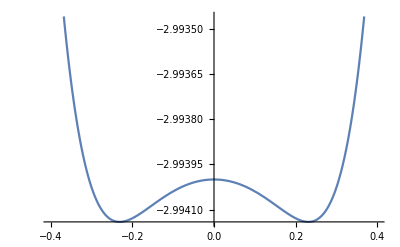
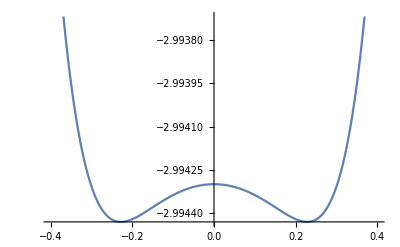
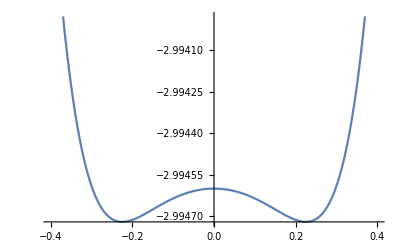
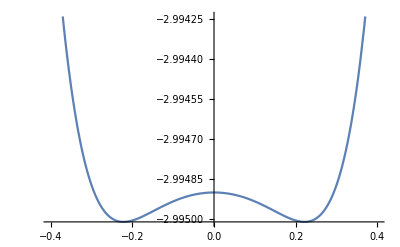
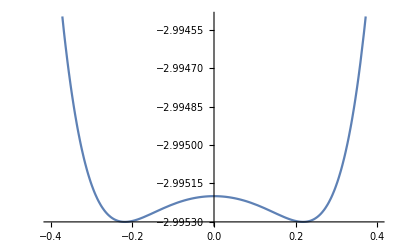
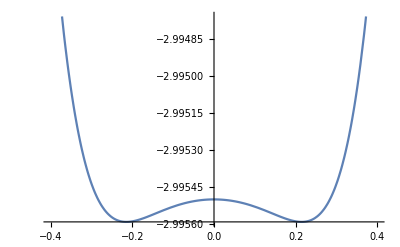
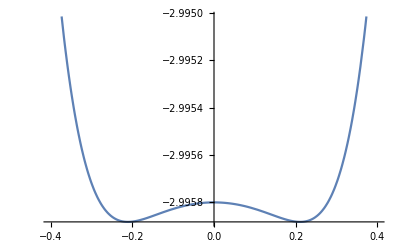
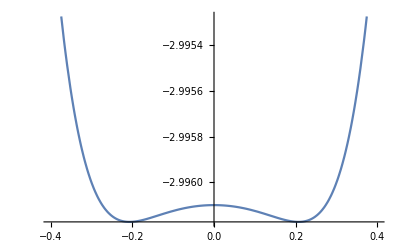

```mathematica
Table[Plot[2 m^2+Root[-16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3&,1],{m,-0.4,0.4}],{Δ,d31}]
```

```mathematica
Series[2 m^2+Root[-16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3&,1],{m,0,8}]
```

Root::sbr: Because of branch cuts, the series may represent a different root of -16 m^2 Δ+3 Δ^3+(-16 m^2-5 Δ^2) #1+Δ #1^2+#1^3& for some values of {Δ,m}.

-3 Δ+(2-2/Δ) m^2+m^6/(2 Δ^5)-m^8/(2 Δ^7)+O[m]^9

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------------------------------------------3-leg, 2-rung MF-----------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H32=-2m (KroneckerProduct[I2,z, I1] + KroneckerProduct[I3,z]) - KroneckerProduct[z,I1,z,I1] -KroneckerProduct[I1,z,I1,z] - Δ(KroneckerProduct[x,I3] + KroneckerProduct[I1,x,I2] + τ (KroneckerProduct[x,x,I2] + KroneckerProduct[I2,x,x]) + KroneckerProduct[I2,x,I1] + KroneckerProduct[I3,x]) //MatrixForm
```

(-2-4 m | -Δ | -Δ | -Δ τ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0
-Δ | 0 | -Δ τ | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ | 0 | 0
-Δ | -Δ τ | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ | 0
-Δ τ | -Δ | -Δ | 2+4 m | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ
-Δ | 0 | 0 | 0 | -4 m | -Δ | -Δ | -Δ τ | -Δ τ | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | -Δ | -2 | -Δ τ | -Δ | 0 | -Δ τ | 0 | 0 | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | -Δ | -Δ τ | 2 | -Δ | 0 | 0 | -Δ τ | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | -Δ τ | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | -4 m | -Δ | -Δ | -Δ τ | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | -Δ τ | 0 | 0 | -Δ | 2 | -Δ τ | -Δ | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ | 0 | -Δ | -Δ τ | -2 | -Δ | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ τ | -Δ τ | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ
-Δ τ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 2-4 m | -Δ | -Δ | -Δ τ
0 | -Δ τ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ τ | -Δ
0 | 0 | -Δ τ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | -Δ τ | 0 | -Δ
0 | 0 | 0 | -Δ τ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ τ | -Δ | -Δ | -2+4 m)

```mathematica
Ham32 = H32/.{τ->1}
```

(-2-4 m | -Δ | -Δ | -Δ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0
-Δ | 0 | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0
-Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0
-Δ | -Δ | -Δ | 2+4 m | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | -4 m | -Δ | -Δ | -Δ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | -Δ | -2 | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | -Δ | -Δ | 2 | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | -Δ | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -4 m | -Δ | -Δ | -Δ | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 2 | -Δ | -Δ | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | -2 | -Δ | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 2-4 m | -Δ | -Δ | -Δ
0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ
0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | 0 | -Δ
0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ | -Δ | -Δ | -2+4 m)

```mathematica
ex32 = Eigenvalues[Ham32];
```

```mathematica
Eigenvalues[({{-2-4 m, -Δ, -Δ, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0}, {-Δ, 0, -Δ, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0}, {-Δ, -Δ, 0, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0}, {-Δ, -Δ, -Δ, 2+4 m, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, -4 m, -Δ, -Δ, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, -Δ, -2, -Δ, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, -Δ, -Δ, 2, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, -Δ, -Δ, -Δ, 4 m, 0, 0, 0, -Δ, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, -Δ, 0, 0, 0, -4 m, -Δ, -Δ, -Δ, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 2, -Δ, -Δ, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, -Δ, -2, -Δ, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, -Δ, -Δ, 4 m, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 2-4 m, -Δ, -Δ, -Δ}, {0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 0, -Δ, -Δ}, {0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, -Δ, 0, -Δ}, {0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, -Δ, -Δ, -2+4 m}})]
```

{2 Δ,Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,1],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,2],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,3],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,4],Root[-32 Δ^5+(64 m^2+64 m^2 Δ^2+16 Δ^4) #1+(8 Δ+16 Δ^3) #1^2+(-4-16 m^2-8 Δ^2) #1^3-2 Δ #1^4+#1^5&,5],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,1],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,2],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,3],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,4],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,5],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,6],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,7],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,8],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,9],Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,10]}

```mathematica
d32 = Range[1.08,1.11,0.001];
```

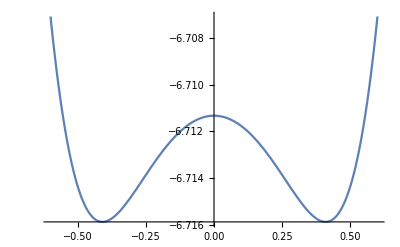
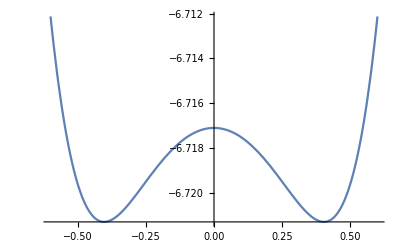
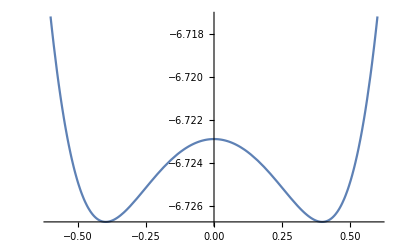
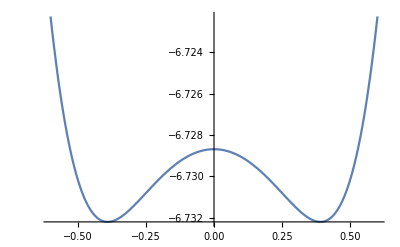
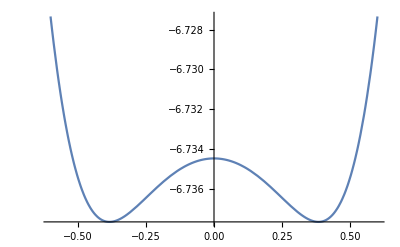
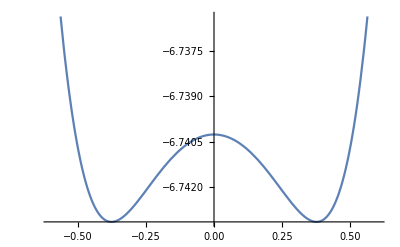
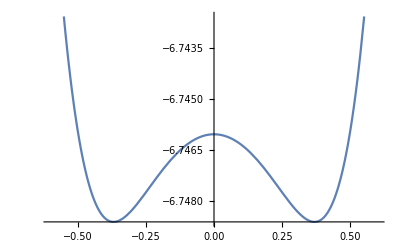
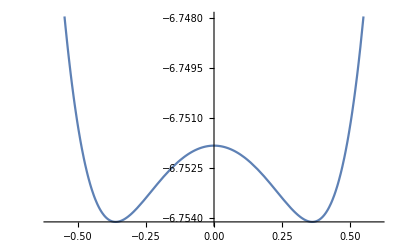

```mathematica
Table[Plot[2 m^2+Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,1],{m,-0.6,0.6}],{Δ,d32}]
```

```mathematica
Table[Series[2 m^2+Root[-16384 m^4 Δ^4+1024 Δ^6+8192 m^2 Δ^6-2048 Δ^8+8192 m^2 Δ^8-3072 Δ^10+(2048 m^2 Δ-16384 m^4 Δ+32768 m^6 Δ+6144 m^2 Δ^3-16384 m^4 Δ^3+1024 Δ^5+6144 m^2 Δ^5-32768 m^4 Δ^5+2048 Δ^7+2048 m^2 Δ^7+1024 Δ^9) #1+(1024 m^2-8192 m^4+16384 m^6-256 Δ^2+9216 m^2 Δ^2-20480 m^4 Δ^2+32768 m^6 Δ^2+256 Δ^4+3072 m^2 Δ^4+12288 m^4 Δ^4+2816 Δ^6+1024 m^2 Δ^6+3328 Δ^8) #1^2+(-256 Δ+512 m^2 Δ-4096 m^4 Δ-8192 m^6 Δ-1024 Δ^3-3072 m^2 Δ^3-1792 Δ^5-3584 m^2 Δ^5-1024 Δ^7) #1^3+(-64-256 m^2-1024 m^4-4096 m^6-320 Δ^2-2048 m^2 Δ^2-6144 m^4 Δ^2-1216 Δ^4-2816 m^2 Δ^4-1408 Δ^6) #1^4+(192 Δ+384 m^2 Δ+2048 m^4 Δ+512 Δ^3+1408 m^2 Δ^3+384 Δ^5) #1^5+(48+192 m^2+768 m^4+208 Δ^2+704 m^2 Δ^2+288 Δ^4) #1^6+(-48 Δ-160 m^2 Δ-64 Δ^3) #1^7+(-12-48 m^2-28 Δ^2) #1^8+4 Δ #1^9+#1^10&,1],{m,0,8}],{Δ,d32}]
```

Series::icm: Series in m to be combined have unequal expansion points 0 and 0..

General::stop: Further output of Series::icm will be suppressed during this calculation.

{(2 m^2+O[m]^9)+(-6.71132-2.04448 (m+0.)^2+0.0299399 (m+0.)^4+0.52629 (m+0.)^6-0.582195 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.71711-2.04222 (m+0.)^2+0.0298058 (m+0.)^4+0.523418 (m+0.)^6-0.577698 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.7229-2.03997 (m+0.)^2+0.0296724 (m+0.)^4+0.520565 (m+0.)^6-0.57324 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.72868-2.03772 (m+0.)^2+0.0295397 (m+0.)^4+0.517731 (m+0.)^6-0.568822 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.73447-2.03548 (m+0.)^2+0.0294078 (m+0.)^4+0.514916 (m+0.)^6-0.564444 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.74026-2.03324 (m+0.)^2+0.0292765 (m+0.)^4+0.51212 (m+0.)^6-0.560104 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.74605-2.03101 (m+0.)^2+0.029146 (m+0.)^4+0.509342 (m+0.)^6-0.555803 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.75184-2.02878 (m+0.)^2+0.0290161 (m+0.)^4+0.506583 (m+0.)^6-0.551541 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.75763-2.02656 (m+0.)^2+0.028887 (m+0.)^4+0.503842 (m+0.)^6-0.547316 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.76342-2.02434 (m+0.)^2+0.0287585 (m+0.)^4+0.501119 (m+0.)^6-0.543129 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.76921-2.02213 (m+0.)^2+0.0286308 (m+0.)^4+0.498414 (m+0.)^6-0.538978 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.775-2.01992 (m+0.)^2+0.0285037 (m+0.)^4+0.495727 (m+0.)^6-0.534865 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.78079-2.01772 (m+0.)^2+0.0283773 (m+0.)^4+0.493058 (m+0.)^6-0.530787 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.78658-2.01552 (m+0.)^2+0.0282515 (m+0.)^4+0.490406 (m+0.)^6-0.526746 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.79237-2.01333 (m+0.)^2+0.0281265 (m+0.)^4+0.487772 (m+0.)^6-0.52274 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.79816-2.01114 (m+0.)^2+0.0280021 (m+0.)^4+0.485155 (m+0.)^6-0.51877 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.80396-2.00896 (m+0.)^2+0.0278783 (m+0.)^4+0.482555 (m+0.)^6-0.514834 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.80975-2.00679 (m+0.)^2+0.0277552 (m+0.)^4+0.479972 (m+0.)^6-0.510933 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.81554-2.00461 (m+0.)^2+0.0276328 (m+0.)^4+0.477406 (m+0.)^6-0.507066 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.82134-2.00245 (m+0.)^2+0.027511 (m+0.)^4+0.474857 (m+0.)^6-0.503233 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.82713-2.00029 (m+0.)^2+0.0273899 (m+0.)^4+0.472324 (m+0.)^6-0.499433 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.83292-1.99813 (m+0.)^2+0.0272694 (m+0.)^4+0.469808 (m+0.)^6-0.495667 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.83872-1.99598 (m+0.)^2+0.0271496 (m+0.)^4+0.467309 (m+0.)^6-0.491934 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.84451-1.99383 (m+0.)^2+0.0270303 (m+0.)^4+0.464825 (m+0.)^6-0.488233 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.85031-1.99169 (m+0.)^2+0.0269117 (m+0.)^4+0.462358 (m+0.)^6-0.484564 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.8561-1.98955 (m+0.)^2+0.0267938 (m+0.)^4+0.459907 (m+0.)^6-0.480927 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.8619-1.98742 (m+0.)^2+0.0266764 (m+0.)^4+0.457472 (m+0.)^6-0.477322 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.8677-1.98529 (m+0.)^2+0.0265597 (m+0.)^4+0.455052 (m+0.)^6-0.473748 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.87349-1.98316 (m+0.)^2+0.0264436 (m+0.)^4+0.452648 (m+0.)^6-0.470204 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.87929-1.98105 (m+0.)^2+0.0263281 (m+0.)^4+0.45026 (m+0.)^6-0.466692 (m+0.)^8+O[m+0.]^9),(2 m^2+O[m]^9)+(-6.88509-1.97893 (m+0.)^2+0.0262132 (m+0.)^4+0.447887 (m+0.)^6-0.46321 (m+0.)^8+O[m+0.]^9)}

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------------------------------------------3-leg, 3-rung MF-----------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H33 = -2m(KroneckerProduct[I3,I2,z]+KroneckerProduct[I3,I1,z,I1]) - KroneckerProduct[z,I1,z,I3] - KroneckerProduct[I1,z,I1,z,I2] - KroneckerProduct[I2,z,I1,z,I1] - KroneckerProduct[I3,z,I1,z] -Δ(KroneckerProduct[x,I3,I2]+ KroneckerProduct[I1,x,I3,I1] + KroneckerProduct[I2,x,I3]+ KroneckerProduct[I3,x,I2]+ KroneckerProduct[I3,I1,x,I1]+ KroneckerProduct[I3,I2,x]+τ(KroneckerProduct[x,x,I3,I1]+KroneckerProduct[I2,x,x,I2]+KroneckerProduct[I3,I1,x,x]));
```

```mathematica
d33 = Range[1.11448,1.11449,.000001]
```

{1.11448,1.11448,1.11448,1.11448,1.11448,1.11449,1.11449,1.11449,1.11449,1.11449,1.11449}

```mathematica
dm33 =  Range[-0.14,0.14,.001];
```

```mathematica
Ham33=N[H33/.{τ->1}];
```

```mathematica
(*Table[ge[[i]]=Flatten[Table[2 m^2+Eigenvalues[Ham33,1],{Δ,d33},{m,dm}][[i+14,All]]]//FullSimplify,{i,1,Length[d33],1}]*)
```

```mathematica
ge33 = Flatten[Table[Sort[2 m^2+Eigenvalues[Ham33]][[1]],{Δ,d33},{m,dm33}][[1,All]]]//FullSimplify;
```

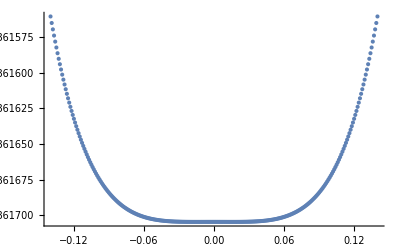

```mathematica
ListPlot[Thread[{dm33, ge33}]]
```

{0.016,0.014,-0.013,0.011,0.01,0.007,-0.004,0.,0.,0.,0.}

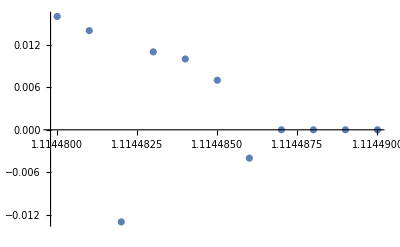

```mathematica
mag33=Table[SortBy[Thread[{dm33,Flatten[Table[Sort[2 m^2+Eigenvalues[Ham33]][[1]],{Δ,d33},{m,dm33}][[i,All]]]}],{Last}][[1,1]],{i,1,Length[d33]}]//FullSimplify
ListPlot[Thread[{d33, mag33}]]
```

```mathematica
data33=Table[{dm33[[i]],ge33[[i]]},{i,1,Length[dm33]}];
```

```mathematica
Fit[data,{1,ϕ^2,ϕ^4,ϕ^6},{ϕ}]
```

-10.4855-0.000193672 ϕ^2+0.0293711 ϕ^4+0.454966 ϕ^6

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------------------------------------------4-leg, 1-rung MF-----------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H41 =-2m(KroneckerProduct[z,I2] + KroneckerProduct[I1,z,I1] + KroneckerProduct[I2,z]) -Δ(KroneckerProduct[x,I2]+ KroneckerProduct[I1,x,I1] + KroneckerProduct[I2,x] + τ KroneckerProduct[x,x,x])//MatrixForm
```

(-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ τ
-Δ | -2 m | 0 | -Δ | 0 | -Δ | -Δ τ | 0
-Δ | 0 | -2 m | -Δ | 0 | -Δ τ | -Δ | 0
0 | -Δ | -Δ | 2 m | -Δ τ | 0 | 0 | -Δ
-Δ | 0 | 0 | -Δ τ | -2 m | -Δ | -Δ | 0
0 | -Δ | -Δ τ | 0 | -Δ | 2 m | 0 | -Δ
0 | -Δ τ | -Δ | 0 | -Δ | 0 | 2 m | -Δ
-Δ τ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 6 m)

```mathematica
Ham41= H41/.{τ->1}
```

(-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | -Δ
-Δ | -2 m | 0 | -Δ | 0 | -Δ | -Δ | 0
-Δ | 0 | -2 m | -Δ | 0 | -Δ | -Δ | 0
0 | -Δ | -Δ | 2 m | -Δ | 0 | 0 | -Δ
-Δ | 0 | 0 | -Δ | -2 m | -Δ | -Δ | 0
0 | -Δ | -Δ | 0 | -Δ | 2 m | 0 | -Δ
0 | -Δ | -Δ | 0 | -Δ | 0 | 2 m | -Δ
-Δ | 0 | 0 | -Δ | 0 | -Δ | -Δ | 6 m)

```mathematica
ev41=Eigenvalues[Ham41]
```

```mathematica
Eigenvalues[({{-6 m, -Δ, -Δ, 0, -Δ, 0, 0, -Δ}, {-Δ, -2 m, 0, -Δ, 0, -Δ, -Δ, 0}, {-Δ, 0, -2 m, -Δ, 0, -Δ, -Δ, 0}, {0, -Δ, -Δ, 2 m, -Δ, 0, 0, -Δ}, {-Δ, 0, 0, -Δ, -2 m, -Δ, -Δ, 0}, {0, -Δ, -Δ, 0, -Δ, 2 m, 0, -Δ}, {0, -Δ, -Δ, 0, -Δ, 0, 2 m, -Δ}, {-Δ, 0, 0, -Δ, 0, -Δ, -Δ, 6 m}})]
```

{-2 m,-2 m,2 m,2 m,-2 √(5 m^2+2 Δ^2-2 √(4 m^4+m^2 Δ^2+Δ^4)),2 √(5 m^2+2 Δ^2-2 √(4 m^4+m^2 Δ^2+Δ^4)),-2 √(5 m^2+2 Δ^2+2 √(4 m^4+m^2 Δ^2+Δ^4)),2 √(5 m^2+2 Δ^2+2 √(4 m^4+m^2 Δ^2+Δ^4))}

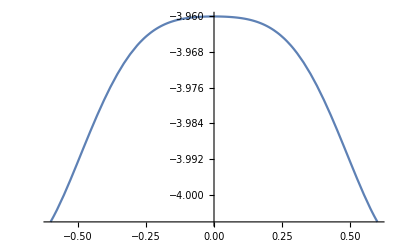
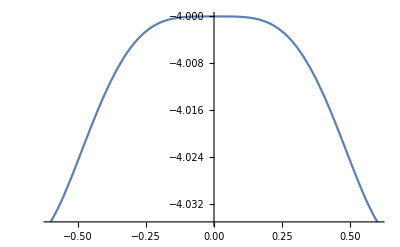
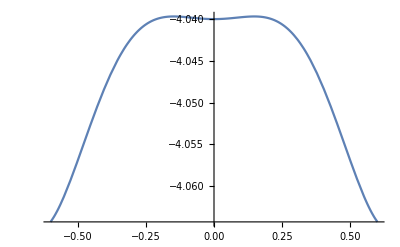
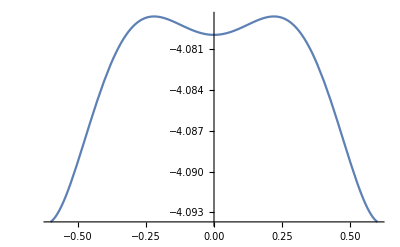
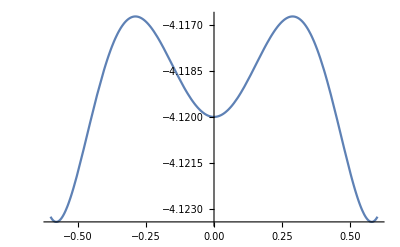
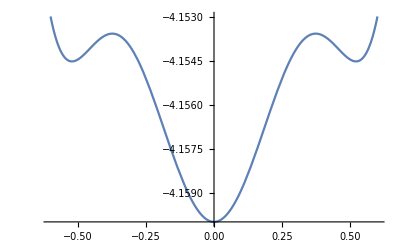
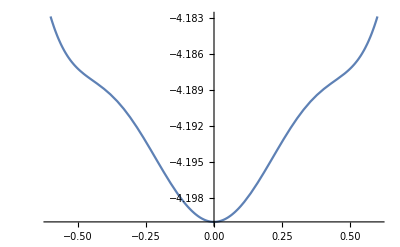
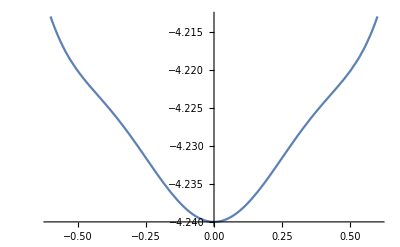

```mathematica
d41 = Range[0.99,1.1,.01];
Table[Plot[3 m^2-2 √(5 m^2+2 Δ^2+2 √(4 m^4+m^2 Δ^2+Δ^4)),{m,-0.6,0.6}],{Δ,d41}]
```

```mathematica
Series[3 m^2-2 √(5 m^2+2 Δ^2+2 √(4 m^4+m^2 Δ^2+Δ^4)),{m,0,6}]
```

-2 (√2 √(Δ^2+√(Δ^4)))+(3-(5+(√(Δ^4))/Δ^2)/(√2 √(Δ^2+√(Δ^4)))) m^2-(√(Δ^2+√(Δ^4)) (15/(4 √(Δ^4) (Δ^2+√(Δ^4)))-((5+(√(Δ^4))/Δ^2)^2)/(8 (Δ^2+√(Δ^4))^2)) m^4)/(√2)-1/3 (√2 √(Δ^2+√(Δ^4)) (-(45 √(Δ^4))/(16 Δ^6 (Δ^2+√(Δ^4)))-(3 (5+(√(Δ^4))/Δ^2) (15/(4 √(Δ^4) (Δ^2+√(Δ^4)))-((5+(√(Δ^4))/Δ^2)^2)/(8 (Δ^2+√(Δ^4))^2)))/(8 (Δ^2+√(Δ^4))))) m^6+O[m]^7

```mathematica
Table[Series[3 m^2-2 √(5 m^2+2 Δ^2+2 √(4 m^4+m^2 Δ^2+Δ^4)),{m,0,6}],{Δ,d41}]
```

{-3.96-0.030303 m^2-0.772958 m^4+1.5773 m^6+O[m]^7,-4.-0.75 m^4+1.5 m^6+O[m]^7,-4.04+0.029703 m^2-0.727943 m^4+1.4272 m^6+O[m]^7,-4.08+0.0588235 m^2-0.706742 m^4+1.3586 m^6+O[m]^7,-4.12+0.0873786 m^2-0.686356 m^4+1.29391 m^6+O[m]^7,-4.16+0.115385 m^2-0.666747 m^4+1.23289 m^6+O[m]^7,-4.2+0.142857 m^2-0.647878 m^4+1.17529 m^6+O[m]^7,-4.24+0.169811 m^2-0.629714 m^4+1.12089 m^6+O[m]^7,-4.28+0.196262 m^2-0.612223 m^4+1.06948 m^6+O[m]^7,-4.32+0.222222 m^2-0.595374 m^4+1.02087 m^6+O[m]^7,-4.36+0.247706 m^2-0.579138 m^4+0.974897 m^6+O[m]^7,-4.4+0.272727 m^2-0.563486 m^4+0.931382 m^6+O[m]^7}

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------4-leg, 1-rung MF complete--------------------------------------*)
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H41c =-2m(KroneckerProduct[z,z,I2] + KroneckerProduct[I1,z,z,I1] + KroneckerProduct[I2,z,z]) -Δ(KroneckerProduct[x,I3]+ KroneckerProduct[I1,x,I2] + KroneckerProduct[I2,x,I1] + KroneckerProduct[I3,x])//MatrixForm
```

(-6 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0
-Δ | -2 m | 0 | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0
-Δ | 0 | 2 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0
0 | -Δ | -Δ | -2 m | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0
-Δ | 0 | 0 | 0 | 2 m | -Δ | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | -Δ | 6 m | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | -Δ | 0 | 2 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | -2 m | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | 0 | -2 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 2 m | 0 | -Δ | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 6 m | -Δ | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | -Δ | -Δ | 2 m | 0 | 0 | 0 | -Δ
0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -2 m | -Δ | -Δ | 0
0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 2 m | 0 | -Δ
0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | 0 | -2 m | -Δ
0 | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | -6 m)

```mathematica
ev41c=Eigenvalues[H41c]
```

```mathematica
Eigenvalues[({{-6 m, -Δ, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, 0}, {-Δ, -2 m, 0, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0}, {-Δ, 0, 2 m, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0}, {0, -Δ, -Δ, -2 m, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0}, {-Δ, 0, 0, 0, 2 m, -Δ, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, -Δ, 6 m, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, -Δ, 0, 2 m, -Δ, 0, 0, 0, 0, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, 0, -Δ, -Δ, -2 m, 0, 0, 0, 0, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, 0, 0, 0, 0, -2 m, -Δ, -Δ, 0, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, 0, 0, 0, 0, -Δ, 2 m, 0, -Δ, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, 0, 6 m, -Δ, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, 0, 0, 0, 0, 0, -Δ, -Δ, 2 m, 0, 0, 0, -Δ}, {0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, -2 m, -Δ, -Δ, 0}, {0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 2 m, 0, -Δ}, {0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, 0, -2 m, -Δ}, {0, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, -Δ, -6 m}})]
```

{-2 m,2 m,-√Root[-576 m^6+(304 m^4+320 m^2 Δ^2) #1+(-44 m^2-16 Δ^2) #1^2+#1^3&,1],√Root[-576 m^6+(304 m^4+320 m^2 Δ^2) #1+(-44 m^2-16 Δ^2) #1^2+#1^3&,1],-√Root[-576 m^6+(304 m^4+320 m^2 Δ^2) #1+(-44 m^2-16 Δ^2) #1^2+#1^3&,2],√Root[-576 m^6+(304 m^4+320 m^2 Δ^2) #1+(-44 m^2-16 Δ^2) #1^2+#1^3&,2],-√Root[-576 m^6+(304 m^4+320 m^2 Δ^2) #1+(-44 m^2-16 Δ^2) #1^2+#1^3&,3],√Root[-576 m^6+(304 m^4+320 m^2 Δ^2) #1+(-44 m^2-16 Δ^2) #1^2+#1^3&,3],Root[48 m^4+16 Δ^4+(16 m^3+16 m Δ^2) #1+(-16 m^2-8 Δ^2) #1^2-4 m #1^3+#1^4&,1],Root[48 m^4+16 Δ^4+(16 m^3+16 m Δ^2) #1+(-16 m^2-8 Δ^2) #1^2-4 m #1^3+#1^4&,2],Root[48 m^4+16 Δ^4+(16 m^3+16 m Δ^2) #1+(-16 m^2-8 Δ^2) #1^2-4 m #1^3+#1^4&,3],Root[48 m^4+16 Δ^4+(16 m^3+16 m Δ^2) #1+(-16 m^2-8 Δ^2) #1^2-4 m #1^3+#1^4&,4],Root[48 m^4+16 Δ^4+(-16 m^3-16 m Δ^2) #1+(-16 m^2-8 Δ^2) #1^2+4 m #1^3+#1^4&,1],Root[48 m^4+16 Δ^4+(-16 m^3-16 m Δ^2) #1+(-16 m^2-8 Δ^2) #1^2+4 m #1^3+#1^4&,2],Root[48 m^4+16 Δ^4+(-16 m^3-16 m Δ^2) #1+(-16 m^2-8 Δ^2) #1^2+4 m #1^3+#1^4&,3],Root[48 m^4+16 Δ^4+(-16 m^3-16 m Δ^2) #1+(-16 m^2-8 Δ^2) #1^2+4 m #1^3+#1^4&,4]}

```mathematica
d41c = Range[0.99,1.04,.01];
```

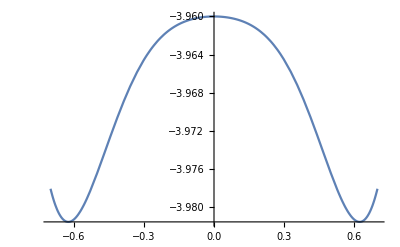
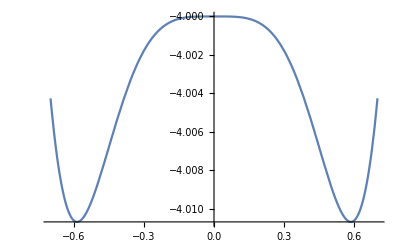
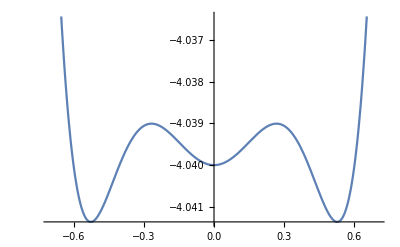
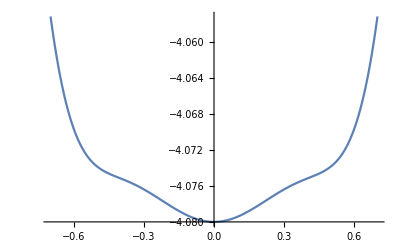
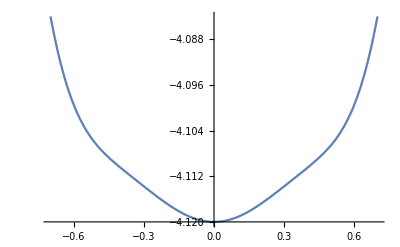
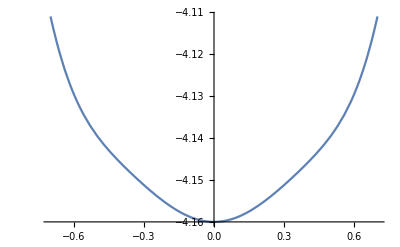

```mathematica
Table[Plot[3 m^2+{-√Root[-576 m^6+(304 m^4+320 m^2 Δ^2) #1+(-44 m^2-16 Δ^2) #1^2+#1^3&,3]},{m,-0.7,0.7}],{Δ,d41c}]
```

```mathematica
Series[3 m^2-√Root[-576 m^6+(304 m^4+320 m^2 Δ^2) #1+(-44 m^2-16 Δ^2) #1^2+#1^3&,3],{m,0,6}]
```

Root::sbr: Because of branch cuts, the series may represent a different root of -576 m^6+(304 m^4+320 m^2 Δ^2) #1+(-44 m^2-16 Δ^2) #1^2+#1^3& for some values of {Δ,m}.

-4 √(Δ^2)+(3-3/(√(Δ^2))) m^2-(√(Δ^2) m^4)/(4 Δ^4)+(√(Δ^2) m^6)/(4 Δ^6)+O[m]^7

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------4-leg, 2-rung MF Complete--------------------------------------*)
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H42c =-2m(KroneckerProduct[I4,z,z,I2]+KroneckerProduct[I4,I1,z,z,I1]+KroneckerProduct[I4,I2,z,z]) - KroneckerProduct[z,z,I2,z,z,I2] - KroneckerProduct[I1,z,z,I2,z,z,I1] - KroneckerProduct[I2,z,z,I2,z,z] -Δ(KroneckerProduct[x,I4,I3]+ KroneckerProduct[I1,x,I4,I2] + KroneckerProduct[I2,x,I4,I1]+ KroneckerProduct[I3,x,I4]+ KroneckerProduct[I4,x,I3]+ KroneckerProduct[I4,I1,x,I2]+ KroneckerProduct[I4,I2,x,I1]+ KroneckerProduct[I4,I3,x]);
```

```mathematica
d42c = Range[1.1,1.13,.005]
```

{1.1,1.105,1.11,1.115,1.12,1.125,1.13}

```mathematica
dm42c = Range[-1,1,.01];
```

```mathematica
(*ListPlot[{Thread[{dm42, gse1}],Thread[{dm42, gse2}],Thread[{dm42, gse3}],Thread[{dm42, gse4}],Thread[{dm42, gse5}],Thread[{dm42, gse6}],Thread[{dm42, gse7}],Thread[{dm42, gse8}],Thread[{dm42, gse9}],Thread[{dm42, gse10}],Thread[{dm42, gse11}],Thread[{dm42, gse12}],Thread[{dm42, gse13}],Thread[{dm42, gse14}],Thread[{dm42, gse15}],Thread[{dm42, gse16}]},AxesLabel->Automatic]*)
```

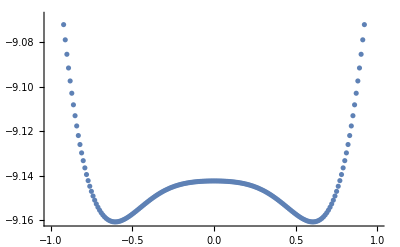

```mathematica
ge42c = Flatten[Table[Sort[3 m^2+Eigenvalues[H42c]][[1]],{Δ,d42c},{m,dm42c}][[1,All]]]//FullSimplify;
 (*gse2 = Flatten[Table[2 m^2+Eigenvalues[Ham33,1],{Δ,d42},{m,dm42}][[44,All]]]//FullSimplify;*)
ListPlot[Thread[{dm42c, ge42c}]]
```

```mathematica
data42c=Table[{dm42c[[i]],ge42c[[i]]},{i,1,Length[dm42c]}];
Fit[data42c,{1,ϕ^2,ϕ^4,ϕ^6},{ϕ}]
```

-9.14064-0.0849678 ϕ^2+0.0174063 ϕ^4+0.207773 ϕ^6

{-0.6,-0.58,0.56,0.52,0.,0.,0.}

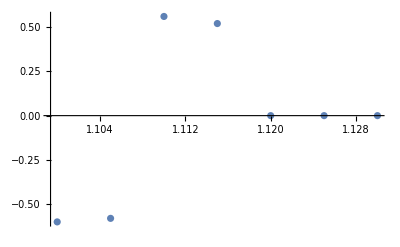

```mathematica
mag42c=Table[SortBy[Thread[{dm42c,Flatten[Table[Sort[3 m^2+Eigenvalues[H42c]][[1]],{Δ,d42c},{m,dm42c}][[i,All]]]}],{Last}][[1,1]],{i,1,Length[d42c]}]//FullSimplify
ListPlot[Thread[{d42c, mag42c}]]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------4-leg, 3-rung MF Complete--------------------------------------*)
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H43c =-2m(KroneckerProduct[I4,I4,z,I3]+KroneckerProduct[I4,I4,I1,z,I2]+KroneckerProduct[I4,I4,I2,z,I1]+KroneckerProduct[I4,I4,I3,z]) - KroneckerProduct[z,I3,z,I3,I4] - KroneckerProduct[I1,z,I3,z,I4,I2] - KroneckerProduct[I2,z,I3,z,I4,I1] - KroneckerProduct[I3,z,I3,z,I4] - KroneckerProduct[I4,z,I3,z,I3] - KroneckerProduct[I4,I1,z,I3,z,I2] - KroneckerProduct[,I4,I2,z,I3,z,I1] - KroneckerProduct[I4,I3,z,I3,z] -Δ(KroneckerProduct[x,I4,I4,I3]+ KroneckerProduct[I1,x,I4,I4,I2] + KroneckerProduct[I2,x,I4,I4,I1]+ KroneckerProduct[I3,x,I4,I4]+ KroneckerProduct[I4,x,I3,I4]+ KroneckerProduct[I4,I1,x,I4,I2]+ KroneckerProduct[I4,I2,x,I4,I1]+ KroneckerProduct[I4,I3,x,I4]+ KroneckerProduct[I4,I4,x,I3]+ KroneckerProduct[I4,I4,I1,x,I2]+ KroneckerProduct[I4,I4,I2,x,I1]+ KroneckerProduct[I4,I4,I3,x]);
```

```mathematica
d43c = Range[1.2,1.3,.01];
```

```mathematica
dm43c = Range[-1,1,.01];
```

```mathematica
ge43c = Flatten[Table[Sort[3 m^2+Eigenvalues[H43c,1]][[1]],{Δ,d43c},{m,dm43c}][[6,All]]]//FullSimplify;
ListPlot[Thread[{dm43c, ge43c}]]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
(*----------------------------------------------5-leg, 1-rung MF-----------------------------------------*)
```

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H51= -2m(KroneckerProduct[z,I3] + KroneckerProduct[I1,z,I2] + KroneckerProduct[I2,z,I1] + KroneckerProduct[I3,z]) -Δ(KroneckerProduct[x,I3]+ KroneckerProduct[I1,x,I2] + KroneckerProduct[I2,x,I1] + KroneckerProduct[I3,x]+ τ KroneckerProduct[x,x,x,x])//MatrixForm
```

(-8 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ
-Δ | -4 m | 0 | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | -Δ τ | 0
-Δ | 0 | -4 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ τ | 0 | 0
0 | -Δ | -Δ | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ τ | 0 | 0 | 0
-Δ | 0 | 0 | 0 | -4 m | -Δ | -Δ | 0 | 0 | 0 | 0 | -Δ τ | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ τ | 0 | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ τ | 0 | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | 4 m | -Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ τ | -4 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | 0 | -Δ τ | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | 0 | -Δ τ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | -Δ τ | 0 | 0 | 0 | 0 | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ
0 | 0 | 0 | -Δ τ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | -Δ | -Δ | 0
0 | 0 | -Δ τ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 4 m | 0 | -Δ
0 | -Δ τ | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | 0 | 4 m | -Δ
-Δ τ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | 8 m)

```mathematica
Ham51=H51/.{τ->1}
```

(-8 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ | -4 m | 0 | -Δ | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | -Δ | 0
-Δ | 0 | -4 m | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0
0 | -Δ | -Δ | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | -Δ | 0 | 0 | 0
-Δ | 0 | 0 | 0 | -4 m | -Δ | -Δ | 0 | 0 | 0 | 0 | -Δ | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ | 0 | 0 | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | 4 m | -Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | -4 m | -Δ | -Δ | 0 | -Δ | 0 | 0 | 0
0 | -Δ | 0 | 0 | 0 | 0 | -Δ | 0 | -Δ | 0 | 0 | -Δ | 0 | -Δ | 0 | 0
0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | -Δ | 0
0 | 0 | 0 | -Δ | -Δ | 0 | 0 | 0 | 0 | -Δ | -Δ | 4 m | 0 | 0 | 0 | -Δ
0 | 0 | 0 | -Δ | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | 0 | -Δ | -Δ | 0
0 | 0 | -Δ | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | 0 | -Δ | 4 m | 0 | -Δ
0 | -Δ | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | 0 | 4 m | -Δ
-Δ | 0 | 0 | 0 | 0 | 0 | 0 | -Δ | 0 | 0 | 0 | -Δ | 0 | -Δ | -Δ | 8 m)

```mathematica
ev51=Eigenvalues[Ham51]
```

```mathematica
Eigenvalues[({{-8 m, -Δ, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, 0, 0, -Δ}, {-Δ, -4 m, 0, -Δ, 0, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, -Δ, 0}, {-Δ, 0, -4 m, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 0, 0}, {0, -Δ, -Δ, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, -Δ, 0, 0, 0}, {-Δ, 0, 0, 0, -4 m, -Δ, -Δ, 0, 0, 0, 0, -Δ, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, -Δ, 0, 0, -Δ, 0, -Δ, 0, 0, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, 0, -Δ, -Δ, 4 m, -Δ, 0, 0, 0, 0, 0, 0, -Δ}, {-Δ, 0, 0, 0, 0, 0, 0, -Δ, -4 m, -Δ, -Δ, 0, -Δ, 0, 0, 0}, {0, -Δ, 0, 0, 0, 0, -Δ, 0, -Δ, 0, 0, -Δ, 0, -Δ, 0, 0}, {0, 0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0, 0, -Δ, 0}, {0, 0, 0, -Δ, -Δ, 0, 0, 0, 0, -Δ, -Δ, 4 m, 0, 0, 0, -Δ}, {0, 0, 0, -Δ, -Δ, 0, 0, 0, -Δ, 0, 0, 0, 0, -Δ, -Δ, 0}, {0, 0, -Δ, 0, 0, -Δ, 0, 0, 0, -Δ, 0, 0, -Δ, 4 m, 0, -Δ}, {0, -Δ, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, 0, 4 m, -Δ}, {-Δ, 0, 0, 0, 0, 0, 0, -Δ, 0, 0, 0, -Δ, 0, -Δ, -Δ, 8 m}})]
```

{-Δ,-Δ,Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,1],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,1],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,1],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,2],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,2],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,2],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,3],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,3],Root[16 m^2 Δ-3 Δ^3+(-16 m^2-5 Δ^2) #1-Δ #1^2+#1^3&,3],Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,1],Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,2],Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,3],Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,4],Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,5]}

```mathematica
d51=Range[0.99,1.12,.01]
```

{0.99,1.,1.01,1.02,1.03,1.04,1.05,1.06,1.07,1.08,1.09,1.1,1.11,1.12}

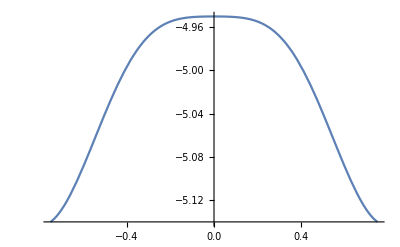
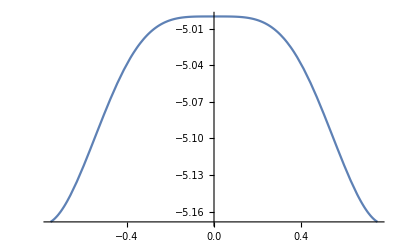
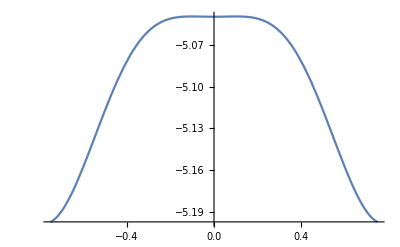
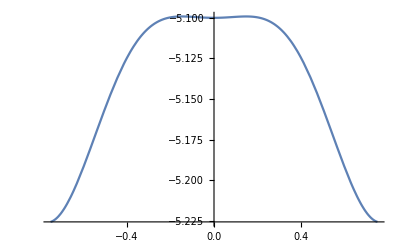
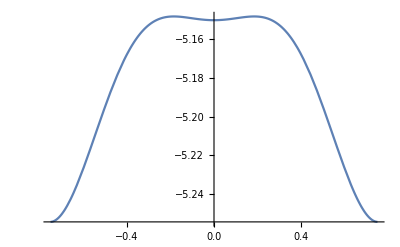
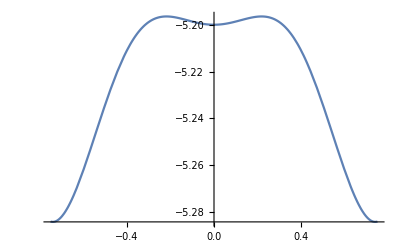
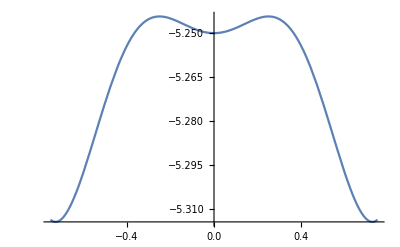
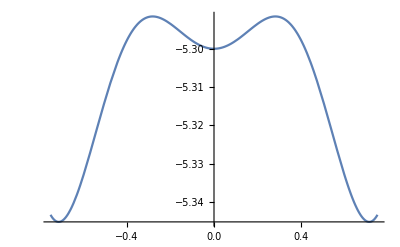

```mathematica
Table[Plot[4 m^2+Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,1],{m,-0.75,0.75}],{Δ,d51}]
```

```mathematica
Series[4 m^2+Root[1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5&,1],{m,0,6}]
```

Root::sbr: Because of branch cuts, the series may represent a different root of 1024 m^4 Δ-944 m^2 Δ^3+45 Δ^5+(1024 m^4+592 m^2 Δ^2+69 Δ^4) #1+(-80 m^2 Δ+2 Δ^3) #1^2+(-80 m^2-22 Δ^2) #1^3+Δ #1^4+#1^5& for some values of {Δ,m}.

-5 Δ+(4-4/Δ) m^2-(2 m^4)/Δ^3+(5 m^6)/(2 Δ^5)+O[m]^7

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------5-leg, 1-rung MF Complete--------------------------------------*)
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H51c= -2m(KroneckerProduct[z,z,I3] + KroneckerProduct[I1,z,z,I2] + KroneckerProduct[I2,z,z,I1] + KroneckerProduct[I3,z,z]) -Δ(KroneckerProduct[x,I4]+ KroneckerProduct[I1,x,I3] + KroneckerProduct[I2,x,I2] + KroneckerProduct[I3,x,I1]+ KroneckerProduct[I4,x]);
```

```mathematica
d51c = Range[1.02,1.05,.001]
dm51c = Range[-1,1,.01];
```

{1.02,1.021,1.022,1.023,1.024,1.025,1.026,1.027,1.028,1.029,1.03,1.031,1.032,1.033,1.034,1.035,1.036,1.037,1.038,1.039,1.04,1.041,1.042,1.043,1.044,1.045,1.046,1.047,1.048,1.049,1.05}

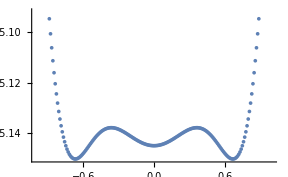

```mathematica
ge51c = Flatten[Table[Sort[4 m^2+Eigenvalues[H51c]][[1]],{Δ,d51c},{m,dm51c}][[10,All]]]//FullSimplify;
 (*gse2 = Flatten[Table[2 m^2+Eigenvalues[Ham33,1],{Δ,d42},{m,dm42}][[44,All]]]//FullSimplify;*)
ListPlot[Thread[{dm51c, ge51c}]]
```

{-0.7,0.69,-0.69,0.69,-0.69,0.68,-0.68,0.68,-0.67,-0.67,0.67,0.66,0.66,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.,0.}

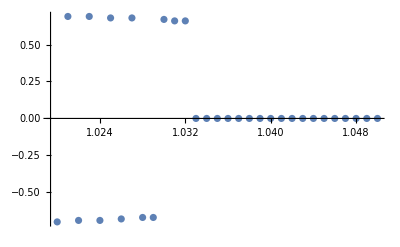

```mathematica
mag51c=Table[SortBy[Thread[{dm51c,Flatten[Table[Sort[4 m^2+Eigenvalues[H51c]][[1]],{Δ,d51c},{m,dm51c}][[i,All]]]}],{Last}][[1,1]],{i,1,Length[d51c]}]//FullSimplify
ListPlot[Thread[{d51c, mag51c}]]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
(*-----------------------------------------5-leg, 2-rung MF Complete--------------------------------------*)
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H51c= -2m(KroneckerProduct[z,z,I3] + KroneckerProduct[I1,z,z,I2] + KroneckerProduct[I2,z,z,I1] + KroneckerProduct[I3,z,z]) -Δ(KroneckerProduct[x,I4]+ KroneckerProduct[I1,x,I3] + KroneckerProduct[I2,x,I2] + KroneckerProduct[I3,x,I1]+ KroneckerProduct[I4,x]);
```

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
(*-----------------------------4-leg, 1-rung MF Complete weak coupling------------------------------------*)
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H41cw =-2m(KroneckerProduct[z,z,I2] + KroneckerProduct[I1,z,z,I1] + δ KroneckerProduct[I2,z,z]) -Δ(KroneckerProduct[x,I3]+ KroneckerProduct[I1,x,I2] + KroneckerProduct[I2,x,I1] + KroneckerProduct[I3,x]);
```

```mathematica
ev41cw=Eigenvalues[H41cw]
```

{-√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,1],√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,1],-√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,2],√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,2],-√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,3],√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,3],-√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,4],√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,4],-√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+2048 m^4 δ^2 Δ^4-512 m^4 δ^4 Δ^4+256 Δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2-512 m^2 Δ^4-256 m^2 δ^2 Δ^4-256 Δ^6) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2+96 Δ^4) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,1],√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+2048 m^4 δ^2 Δ^4-512 m^4 δ^4 Δ^4+256 Δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2-512 m^2 Δ^4-256 m^2 δ^2 Δ^4-256 Δ^6) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2+96 Δ^4) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,1],-√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+2048 m^4 δ^2 Δ^4-512 m^4 δ^4 Δ^4+256 Δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2-512 m^2 Δ^4-256 m^2 δ^2 Δ^4-256 Δ^6) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2+96 Δ^4) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,2],√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+2048 m^4 δ^2 Δ^4-512 m^4 δ^4 Δ^4+256 Δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2-512 m^2 Δ^4-256 m^2 δ^2 Δ^4-256 Δ^6) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2+96 Δ^4) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,2],-√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+2048 m^4 δ^2 Δ^4-512 m^4 δ^4 Δ^4+256 Δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2-512 m^2 Δ^4-256 m^2 δ^2 Δ^4-256 Δ^6) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2+96 Δ^4) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,3],√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+2048 m^4 δ^2 Δ^4-512 m^4 δ^4 Δ^4+256 Δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2-512 m^2 Δ^4-256 m^2 δ^2 Δ^4-256 Δ^6) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2+96 Δ^4) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,3],-√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+2048 m^4 δ^2 Δ^4-512 m^4 δ^4 Δ^4+256 Δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2-512 m^2 Δ^4-256 m^2 δ^2 Δ^4-256 Δ^6) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2+96 Δ^4) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,4],√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+2048 m^4 δ^2 Δ^4-512 m^4 δ^4 Δ^4+256 Δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2-512 m^2 Δ^4-256 m^2 δ^2 Δ^4-256 Δ^6) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2+96 Δ^4) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,4]}

```mathematica
d41cw1 = Range[0.9950746273,0.9950746277,.0000000001];
Length[d41cw]
```

11

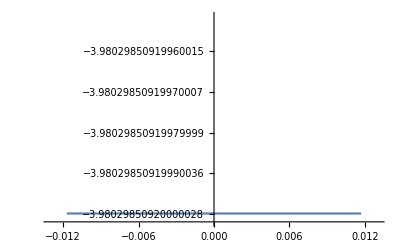
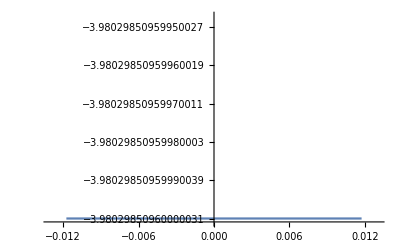
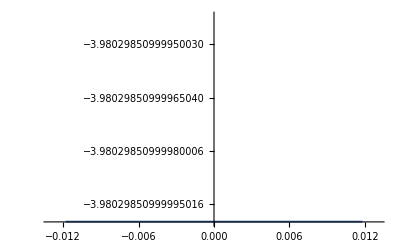
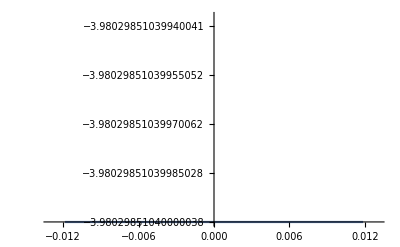
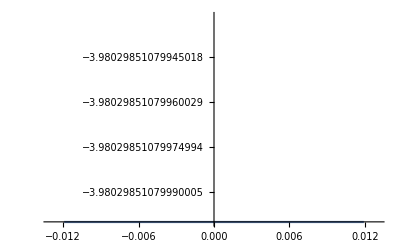

```mathematica
Table[Plot[{(2+δ)m^2+{-√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,4]}}/. {δ->0.01},{m,-0.013,0.013}],{Δ,d41cw1}]
```

```mathematica
d41cw2 = Range[0.95714,0.95715,.000001];
Length[d41cw2]
```

11

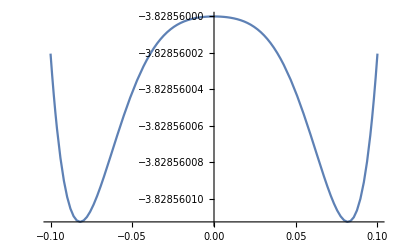
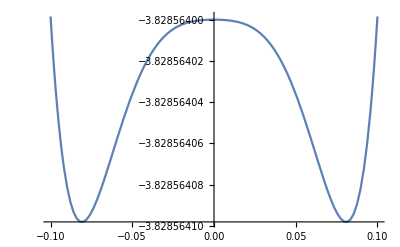
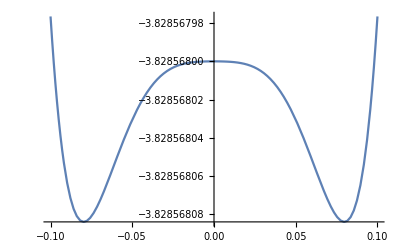
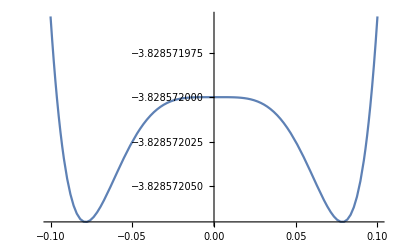
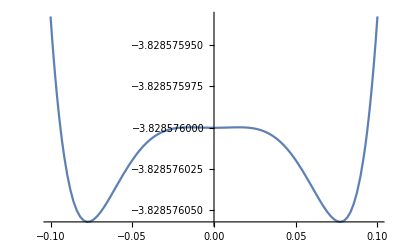
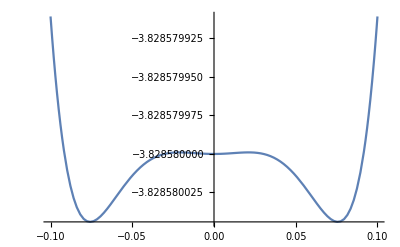
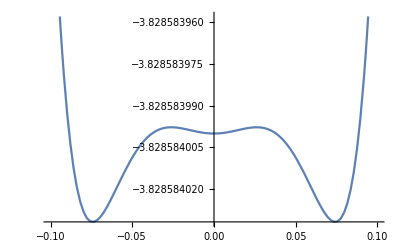
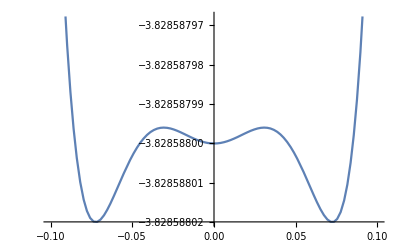

```mathematica
Table[Plot[{(2+δ)m^2+{-√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,4]}}/. {δ->0.1},{m,-0.1,0.1}],{Δ,d41cw2}]
```

```mathematica
Series[{(2+δ)m^2+{-√Root[4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4&,4]}},{m,0,6}]
```

Root::sbr: Because of branch cuts, the series may represent a different root of 4096 m^8 δ^4-2048 m^8 δ^6+256 m^8 δ^8+(-2048 m^6 δ^2+512 m^6 δ^4-256 m^6 δ^6-1024 m^4 Δ^2-256 m^4 δ^4 Δ^2) #1+(256 m^4+128 m^4 δ^2+96 m^4 δ^4+256 m^2 Δ^2+128 m^2 δ^2 Δ^2) #1^2+(-32 m^2-16 m^2 δ^2-16 Δ^2) #1^3+#1^4& for some values of {δ,Δ,m}.

{{-4 √(Δ^2)+(2+δ-(2+δ^2)/(√(Δ^2))) m^2-(-((2+δ^2)^2)/(8 Δ^4)+(4+8 δ^2-δ^4)/(8 Δ^4)) √(Δ^2) m^4-2/3 (((3 (-8+12 δ^2-6 δ^4+δ^6))/(32 Δ^6)-(3 (2+δ^2) (-((2+δ^2)^2)/(8 Δ^4)+(4+8 δ^2-δ^4)/(8 Δ^4)))/(8 Δ^2)) √(Δ^2)) m^6+O[m]^7}}

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
(*------------------------4-leg, 1-rung MF Complete weak coupling middle-leg------------------------------*)
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H41cwc =-2m(KroneckerProduct[z,z,I2] + δ KroneckerProduct[I1,z,z,I1] + KroneckerProduct[I2,z,z]) -Δ(KroneckerProduct[x,I3]+ KroneckerProduct[I1,x,I2] + KroneckerProduct[I2,x,I1] + KroneckerProduct[I3,x]);
```

```mathematica
ev41cwc=Eigenvalues[H41cwc]
```

{-2 m δ,2 m δ,-√Root[-1024 m^6 δ^2+512 m^6 δ^4-64 m^6 δ^6+(256 m^4+48 m^4 δ^4+256 m^2 Δ^2+64 m^2 δ^2 Δ^2) #1+(-32 m^2-12 m^2 δ^2-16 Δ^2) #1^2+#1^3&,1],√Root[-1024 m^6 δ^2+512 m^6 δ^4-64 m^6 δ^6+(256 m^4+48 m^4 δ^4+256 m^2 Δ^2+64 m^2 δ^2 Δ^2) #1+(-32 m^2-12 m^2 δ^2-16 Δ^2) #1^2+#1^3&,1],-√Root[-1024 m^6 δ^2+512 m^6 δ^4-64 m^6 δ^6+(256 m^4+48 m^4 δ^4+256 m^2 Δ^2+64 m^2 δ^2 Δ^2) #1+(-32 m^2-12 m^2 δ^2-16 Δ^2) #1^2+#1^3&,2],√Root[-1024 m^6 δ^2+512 m^6 δ^4-64 m^6 δ^6+(256 m^4+48 m^4 δ^4+256 m^2 Δ^2+64 m^2 δ^2 Δ^2) #1+(-32 m^2-12 m^2 δ^2-16 Δ^2) #1^2+#1^3&,2],-√Root[-1024 m^6 δ^2+512 m^6 δ^4-64 m^6 δ^6+(256 m^4+48 m^4 δ^4+256 m^2 Δ^2+64 m^2 δ^2 Δ^2) #1+(-32 m^2-12 m^2 δ^2-16 Δ^2) #1^2+#1^3&,3],√Root[-1024 m^6 δ^2+512 m^6 δ^4-64 m^6 δ^6+(256 m^4+48 m^4 δ^4+256 m^2 Δ^2+64 m^2 δ^2 Δ^2) #1+(-32 m^2-12 m^2 δ^2-16 Δ^2) #1^2+#1^3&,3],Root[64 m^4 δ^2-16 m^4 δ^4+16 Δ^4+(16 m^3 δ^3+16 m δ Δ^2) #1+(-16 m^2-8 Δ^2) #1^2-4 m δ #1^3+#1^4&,1],Root[64 m^4 δ^2-16 m^4 δ^4+16 Δ^4+(16 m^3 δ^3+16 m δ Δ^2) #1+(-16 m^2-8 Δ^2) #1^2-4 m δ #1^3+#1^4&,2],Root[64 m^4 δ^2-16 m^4 δ^4+16 Δ^4+(16 m^3 δ^3+16 m δ Δ^2) #1+(-16 m^2-8 Δ^2) #1^2-4 m δ #1^3+#1^4&,3],Root[64 m^4 δ^2-16 m^4 δ^4+16 Δ^4+(16 m^3 δ^3+16 m δ Δ^2) #1+(-16 m^2-8 Δ^2) #1^2-4 m δ #1^3+#1^4&,4],Root[64 m^4 δ^2-16 m^4 δ^4+16 Δ^4+(-16 m^3 δ^3-16 m δ Δ^2) #1+(-16 m^2-8 Δ^2) #1^2+4 m δ #1^3+#1^4&,1],Root[64 m^4 δ^2-16 m^4 δ^4+16 Δ^4+(-16 m^3 δ^3-16 m δ Δ^2) #1+(-16 m^2-8 Δ^2) #1^2+4 m δ #1^3+#1^4&,2],Root[64 m^4 δ^2-16 m^4 δ^4+16 Δ^4+(-16 m^3 δ^3-16 m δ Δ^2) #1+(-16 m^2-8 Δ^2) #1^2+4 m δ #1^3+#1^4&,3],Root[64 m^4 δ^2-16 m^4 δ^4+16 Δ^4+(-16 m^3 δ^3-16 m δ Δ^2) #1+(-16 m^2-8 Δ^2) #1^2+4 m δ #1^3+#1^4&,4]}

```mathematica
d41cwc = Range[0.95713,0.95714,.000001];
Length[d41cwc]
```

11

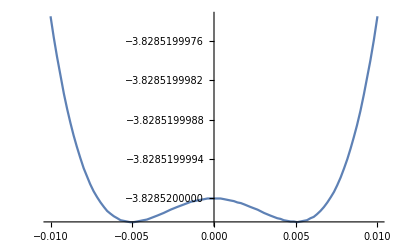
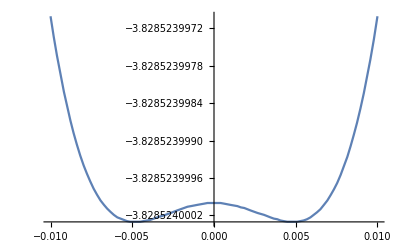
{-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-,-Graphics-}

```mathematica
Table[Plot[{(2+δ)m^2+{-√Root[-1024 m^6 δ^2+512 m^6 δ^4-64 m^6 δ^6+(256 m^4+48 m^4 δ^4+256 m^2 Δ^2+64 m^2 δ^2 Δ^2) #1+(-32 m^2-12 m^2 δ^2-16 Δ^2) #1^2+#1^3&,3]}}/. {δ->0.1},{m,-0.01,0.01}],{Δ,d41cwc}]
```

```mathematica
Series[{(2+δ)m^2+{-√Root[-1024 m^6 δ^2+512 m^6 δ^4-64 m^6 δ^6+(256 m^4+48 m^4 δ^4+256 m^2 Δ^2+64 m^2 δ^2 Δ^2) #1+(-32 m^2-12 m^2 δ^2-16 Δ^2) #1^2+#1^3&,3]}},{m,0,6}]
```

Root::sbr: Because of branch cuts, the series may represent a different root of -1024 m^6 δ^2+512 m^6 δ^4-64 m^6 δ^6+(256 m^4+48 m^4 δ^4+256 m^2 Δ^2+64 m^2 δ^2 Δ^2) #1+(-32 m^2-12 m^2 δ^2-16 Δ^2) #1^2+#1^3& for some values of {δ,Δ,m}.

{{-4 √(Δ^2)+(2+δ-(2+δ^2)/(√(Δ^2))) m^2-(-((2+δ^2)^2)/(8 Δ^4)+(12 δ^2-δ^4)/(8 Δ^4)) √(Δ^2) m^4-2/3 (((3 (8 δ^2-10 δ^4+δ^6))/(32 Δ^6)-(3 (2+δ^2) (-((2+δ^2)^2)/(8 Δ^4)+(12 δ^2-δ^4)/(8 Δ^4)))/(8 Δ^2)) √(Δ^2)) m^6+O[m]^7}}

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
(*-----------------------------4-leg, 2-rung MF Complete weak coupling------------------------------------*)
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
H42cw =-2m(KroneckerProduct[I4,z,z,I2]+KroneckerProduct[I4,I1,z,z,I1]+δ KroneckerProduct[I4,I2,z,z]) - KroneckerProduct[z,z,I2,z,z,I2] - KroneckerProduct[I1,z,z,I2,z,z,I1] - KroneckerProduct[I2,z,z,I2,z,z] -Δ(KroneckerProduct[x,I4,I3]+ KroneckerProduct[I1,x,I4,I2] + KroneckerProduct[I2,x,I4,I1]+ KroneckerProduct[I3,x,I4]+ KroneckerProduct[I4,x,I3]+ KroneckerProduct[I4,I1,x,I2]+ KroneckerProduct[I4,I2,x,I1]+ KroneckerProduct[I4,I3,x]);
```

```mathematica
ev42cw=Eigenvalues[H42cw]
```

$Aborted

```mathematica
Integrate[Sqrt[a-b Cos[k]],{k}]
```

Integrate::ilim: Invalid integration variable or limit(s) in {k}.

```mathematica
Integrate[√(a-b Cos[k]),k]
```

(2 √(a-b Cos[k]) EllipticE[k/2,-(2 b)/(a-b)])/(√((a-b Cos[k])/(a-b)))

```mathematica
ConditionalExpression[2 √(a+b) EllipticE[(2 b)/(a+b)],(Re[a/b]≥1||Re[a/b]≤-1||a/b∉Reals)&&Re[a+b]>0]
```

```mathematica
Manipulate[Plot[(2 √(a-b Cos[x]) EllipticE[x/2,-(2 b)/(a-b)])/(√((a-b Cos[x])/(a-b))),{x,-π,π}],{a,-1.81993,1.81993},{b,-2,2}]
```

```mathematica
Manipulate[Plot[16 x^5 - 8 g^2x^3+8g+g^4x^2+2g^3,{x,0,1}],{g,0,3}]
```

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
(*--------------------------------------------from delta side------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
Plot[x^2 - (2/π)(2x) EllipticE[0],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(2x+0.5) EllipticE[(√(4x))/(2x+0.5)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(2x+1.1) EllipticE[(√(8.8x))/(2x+1.1)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(2x+1.15) EllipticE[(√(9.2x))/(2x+1.15)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(2x+1.16) EllipticE[(√(9.28x))/(2x+1.16)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(2x+1.2) EllipticE[(√(9.6x))/(2x+1.2)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(2x+1.8) EllipticE[(√(12.4x))/(2x+1.8)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(2x+1.9) EllipticE[(√(15.2x))/(2x+1.9)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(2x+2) EllipticE[(√(16x))/(2x+2)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(2x+10) EllipticE[(√(80x))/(2x+10)],{x,0,1.2}]
```

-Graphics-

```mathematica
(*-------------------------------------------------------------------------------------------------------*)
(*--------------------------------------------from J side------------------------------------------------*)
(*-------------------------------------------------------------------------------------------------------*)
```

```mathematica
Plot[x^2 - (2/π) EllipticE[0],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(1.8x+1) EllipticE[(√(7.2x))/(1.8x+1)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(1.86x+1) EllipticE[(√(7.44x))/(1.86x+1)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(1.88x+1) EllipticE[(√(7.52x))/(1.88x+1)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(1.9x+1) EllipticE[(√(7.6x))/(1.9x+1)],{x,0,1.2}]
```

-Graphics-

```mathematica
Plot[x^2 - (2/π)(2x+1) EllipticE[(√(8x))/(2x+1)],{x,0,1.2}]
```

-Graphics-

```mathematica
Integrate[(A^2+B^2-2AB cos[k])^(1/2),k]
```

∫√(A^2+B^2-2 AB cos[k])ⅆk

```mathematica
Integrate[√(A^2+B^2-2AB Cos[k]),{k,-π,π}]
```

ConditionalExpression[4 √(A^2+2 AB+B^2) EllipticE[(4 AB)/(A^2+2 AB+B^2)],(Re[(A^2+B^2)/AB]≥2||Re[(A^2+B^2)/AB]≤-2||(A^2+B^2)/AB∉ℝ)&&Re[A^2+2 AB+B^2]>0]